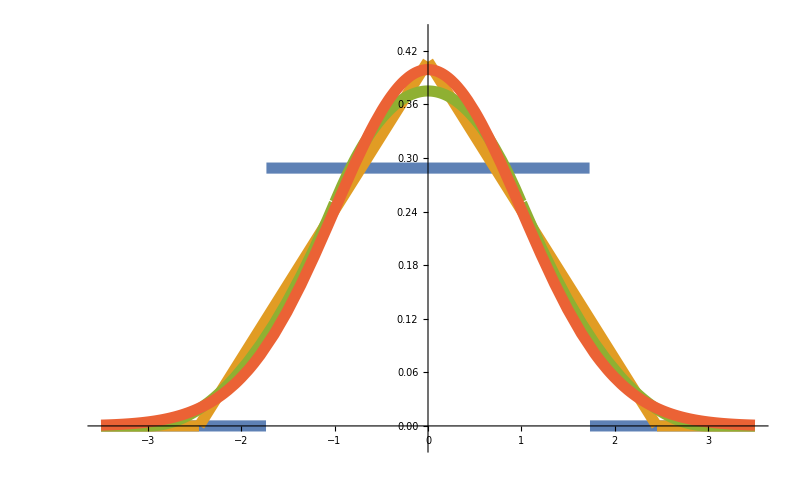

```mathematica
createNormalizedDist[n_]:=Module[{rawDist,mean,stdDev},rawDist=TransformedDistribution[Sum[x[i],{i,1,n}],Table[x[i]\[Distributed]UniformDistribution[{0,1}],{i,1,n}]];
mean=Mean[rawDist];
stdDev=StandardDeviation[rawDist];
TransformedDistribution[(X-mean)/stdDev,X\[Distributed]rawDist]];

(*Create plot with all distributions*)
Plot[Evaluate@Flatten[{Evaluate@Table[PDF[createNormalizedDist[n],x],{n,{1,2,3}}],PDF[NormalDistribution[0,1],x]}],{x,-3.5,3.5},PlotRange->{-.02,.44},PlotStyle->{Thickness[0.01]},BaseStyle->{FontSize->12},ImageSize->800]
```